Which characters should appear in the pullback?
Before we take the pullback it would be nice to reduce the characters that would appear in the Coset CFT character expansion in TIsing^2 characters.

```mathematica
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
hvfs[i_,s_]:=2hv@@i + s+1;
hvft[i_,s_]:=3/2 cv/24+1/2 hv@@i+1/2 s+1
hvf[i_,j_]:=hv@@i+hv@@j;
H={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4}};

Hf=Tuples[H,2];
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_]:=ⅇ^(2 π ⅈ (hv[a[[1]],a[[2]]]-cv/24));
ηv[a_]:=(-1)^(a[[1]]+1);

ηinv[q_,N_:∞]:=∑_(k=0)^N PartitionsP[k] q^k;
χv[r_,s_,q_,N_:∞,e_:1,f_:1]:=Series[ηinv[f q^e](f q^e)^(-1/24-(r s)/2+(p r^2)/(4 p')+(s^2 p')/(4 p))∑_(n=-N)^N ((f q^e)^(n^2 p p'+n (p r-s p'))-(f q^e)^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvI[r_,s_,q_,N_:∞,e_:1,f_:1]:=Series[ηinv[f q^e]∑_(n=-N)^N ((f q^e)^(n^2 p p'+n (p r-s p'))-(f q^e)^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvf[i_,j_,q_,N_]:=χv[i[[1]],i[[2]],q,N]χv[j[[1]],j[[2]],q,N];
χvt[i_,q_,N_]:=If[i[[3]]==0,χvf[i[[1]],i[[2]],q,N], If[Abs[i[[3]]]==1, 1/2(χvf[i[[1]],i[[2]],q,N] + i[[3]] χv[i[[1,1]],i[[1,2]],q,N,2]), 1/2(χv[i[[1,1]],i[[1,2]],q,N,1/2] + i[[3]]/2 tv[i[[1]]]^(-1/2) χv[i[[1,1]],i[[1,2]],q,N,1/2,-1]) ]];
```

c =   7/10

```mathematica
k=8;
cw=(2(k-1))/(k+2);
hw[l_,m_]:=(l(l+2))/(4(k+2))-m^2/(4k);
χw[l_,m_,q_,N_:∞]:=Series[ηinv[q]^2∑_(r=0)^N ∑_(s=0)^N (-1)^(r+s)(q^(1/2 (r^2+s (1+l-m+s)+r (1+l+m+18 s)))-q^(1/2 (18+r^2+s (19+m+s)-l (2+r+s)+r (19-m+18 s)))),{q,0,N}];
χM[A_,q_,χ_,N_:∞]:=χ[A[[1,1]],A[[1,2]],q,N]χ[A[[2,1]],A[[2,2]],q,N];
(*This is the super ugly way to calculate which are the possible values l,m without degeneracies*)
w=ConstantArray[0,{k+1,2k+1}];
M[m_]:=m+k+1;
L[l_]:=l+1
For[l=0,l<=k,l++,For[m=-l,m<=l,m=m+2,If[w[[L[l],M[m]]]==0,w[[L[l],M[m]]]=1;If[0<M[k-m]<=2k+1,w[[L[k-l],M[k-m]]]=-1];If[0<M[k+m]<=2k+1,w[[L[k-l],M[k+m]]]=-1];]]]
W={#[[1]]-1,#[[2]]-k-1}&/@Position[w,_?(# ==1&),{2}];
```

The conformal weights of the two models

TIsing^2

```mathematica
Sort[hvf @@@Hf]
```

{0,3/80,3/80,3/40,1/10,1/10,11/80,11/80,1/5,7/16,7/16,19/40,19/40,43/80,43/80,3/5,3/5,51/80,51/80,7/10,7/10,7/8,83/80,83/80,6/5,3/2,3/2,123/80,123/80,8/5,8/5,31/16,31/16,21/10,21/10,3}

TIsing^2 Invariant subspace

```mathematica
twistedWeights=(hvf@@@Hf)~Join~(hvfs[#,-1]& /@H)~Join~(hvft[#,-1]& /@H)~Join~(hvft[#,1]& /@H)
```

{0,1/10,3/5,3/2,3/80,7/16,1/10,1/5,7/10,8/5,11/80,43/80,3/5,7/10,6/5,21/10,51/80,83/80,3/2,8/5,21/10,3,123/80,31/16,3/80,11/80,51/80,123/80,3/40,19/40,7/16,43/80,83/80,31/16,19/40,7/8,1,6/5,11/5,4,43/40,15/8,87/160,19/32,27/32,207/160,9/16,61/80,7/160,3/32,11/32,127/160,1/16,21/80}

```mathematica
wzwWeights = hw @@@W
```

{7/160,3/40,1/5,3/32,11/32,11/32,1/10,19/40,3/5,19/40,3/32,19/32,27/32,27/32,19/32,3/40,7/10,43/40,6/5,43/40,7/10,7/160,127/160,207/160,247/160,247/160,207/160,127/160,0,7/8,3/2,15/8,2,15/8,3/2,7/8}

```mathematica
search =DeleteDuplicates[Sort[Mod[twistedWeights,1]]]
```

{0,3/80,7/160,1/16,3/40,3/32,1/10,11/80,1/5,21/80,47/160,11/32,7/16,19/40,1/2,43/80,87/160,9/16,19/32,3/5,51/80,7/10,61/80,127/160,27/32,7/8,15/16}

```mathematica
keys = DeleteDuplicates[Sort[Mod[wzwWeights,1]]]
```

{0,7/160,3/40,3/32,1/10,1/5,47/160,11/32,19/40,1/2,87/160,19/32,3/5,7/10,127/160,27/32,7/8}

```mathematica
Total[MemberQ[search,#]&/@keys]
```

17 True

The S-Matrix of the Z_2 Orbifold TIM^2

```mathematica
(* We start by defining an index map *)i=({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);
(* This is the ugliest way I can write down the s-matrix of this thing *)s[a_,b_]:= (sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]a[[3]]Abs[b[[3]]]-1+sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+1/8 a[[3]]b[[3]] tv[a[[1]]]^(1/2)Sum[sv[a[[1]],H[[i]]] tv[H[[i]]]^2 sv[H[[i]],b[[1]]],{i,Length[H]}] tv[b[[1]]]^(1/2)Abs[a[[3]]]-2 Abs[b[[3]]]-2;
So=Array[s[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}] // FullSimplify;

(* Here is a T matrix *)
To=DiagonalMatrix[Array[(tv[i[[#]][[1]]]tv[i[[#]][[2]]](1-Abs[i[[#]][[3]]]-2)+ⅇ^(2 π ⅈ(hvft[i[[#,1]],i[[#,3]]/2]-2 cv/24))Abs[i[[#]][[3]]]-2)&,{Length[i]}]] // FullSimplify;
```

```mathematica
Show[GraphicsRow[MapThread[Legended[#1,Placed[#2,Below]]&,{{MatrixPlot[So,ImageSize->Full],MatrixPlot[To,ImageSize->Full]},{"S matrix", "T matrix"}}],Spacings->0],PlotLabel->HoldForm[S and T matrices],LabelStyle->{GrayLevel[0]},ImageSize->Large]
```

-Graphics-

-Graphics-

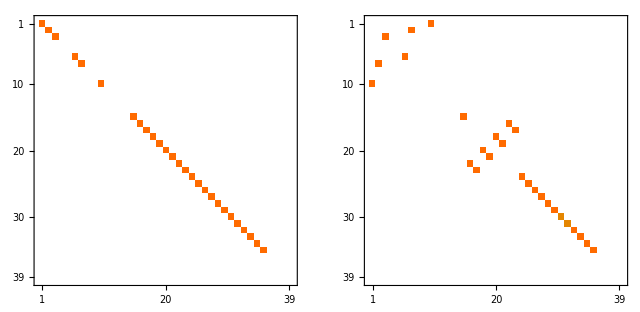

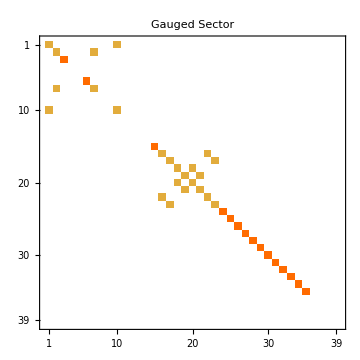

```mathematica
X = So . To;
Mv=DiagonalMatrix[Array[ηv[i[[#,1]]]ηv[i[[#,2]]](1-Abs[i[[#,3]]]-2)+ηv[i[[#,1]]]Abs[i[[#,3]]]-2&,{Length[i]}]];
Mvt= Chop[N[X† . Mv . X] ];
Mv'=So . Mv . So // FullSimplify;

Show[GraphicsRow[MapThread[Legended[MatrixPlot[#1,ImageSize->Full],Placed[#2,Below]]&,{{IdentityMatrix[Length[i]],Mv,Mv' ,Mvt },{"𝟙,𝟙","𝟙,η","η,𝟙","η,η"}}]],ImageSize->Full,PlotLabel->HoldForm["Individual Sectors"],LabelStyle->{GrayLevel[0]}]
GraphicsRow[{1/2(IdentityMatrix[Length[i]] + Mv) // MatrixPlot,1/2 Chop[(Mv' + Mvt)] // MatrixPlot}]
MM = Chop[1/2(IdentityMatrix[Length[i]]  + Mv + Mv'+Mvt)];
MatrixPlot[MM,PlotLabel->"Gauged Sector",ImageSize->Medium,LabelStyle->{GrayLevel[0]}]
```

```mathematica
(* Now Let's calculate the Partition Function *)
n=10;
Xvt = Assuming[q>0,χvt[#,q,n]]&/@i;
Series[Chop[N[Xvt . Xvt]],{q,0,1}]//Echo[#,"Z_σ(q) = "]&;
Series[Chop[Xvt . MM . Xvt],{q,0,1}]//Echo[#,"Z_(σ, η)(q) = "]&;
```

Z_σ(q) =   1/q^(7/60)+1/q^(1/24)+1/q^(7/240)+q^(1/120)+q^(1/30)+q^(17/240)+q^(1/12)+q^(19/120)+q^(17/60)+q^(49/120)+q^(137/240)+q^(91/120)+q^(5/6)+3. q^(23/24)+2. q^(233/240)+5. q^(121/120)+2. q^(31/30)+3. q^(257/240)+3. q^(13/12)+5. q^(139/120)+3. q^(77/60)+3. q^(169/120)+q^(353/240)+5. q^(377/240)+q^(49/30)+2. q^(211/120)+4. q^(11/6)+2. q^(113/60)+12. q^(47/24)+5. q^(473/240)+O[q]^2

Z_(σ, η)(q) =   1/q^(7/60)+2./q^(7/240)+2. q^(1/30)+2. q^(17/240)+q^(1/12)+q^(17/60)+2. q^(137/240)+2. q^(5/6)+4. q^(233/240)+4. q^(31/30)+6. q^(257/240)+3 q^(13/12)+6. q^(77/60)+2. q^(353/240)+10. q^(377/240)+2. q^(49/30)+8. q^(11/6)+2 q^(113/60)+10. q^(473/240)+O[q]^2

Now let’s find the compatible combinations of characters (This doesn’t work anymore because I am moving things around)

```mathematica
nonNegInt[x_]:=IntegerQ[x]&&x>=0
Wpairs=Tuples[W,2];
Hfpairs=Tuples[Hf,2];
weightsM=Sort[DeleteDuplicates[(hw@@#1+hw@@#2)&@@@Wpairs]];
allowedModules=Function[h,{h,Hfpairs[[Position[Hfpairs,_?(nonNegInt[(hvf@@#1+hvf@@#2)&@@# - h]&),1]//Flatten]]}]/@weightsM;
weightsToModules=Function[h,{h,Wpairs[[Position[Wpairs,_?((hw@@#1+hw@@#2)&@@# == h&),1]//Flatten]]}]/@weightsM;
```

```mathematica
n=10;
i=62;
h=allowedModules[[i,1]];
min= Min[(hvf@@#1+hvf@@#2)&@@#-h &/@allowedModules[[i,2]]];
cpf=DeleteDuplicates[q^(-Min[min,0])χM[#,q,χw,n]&/@weightsToModules[[i,2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#1+hvf@@#2)&@@#-h+Min[min,0])χM[#,q,χvf,n]&/@allowedModules[[i,2]]];
Coefficients[allowedModules_,weightsToModules_,n_:10]:=(
h=allowedModules[[1]];
min= Min[(hvf@@#1+hvf@@#2)&@@#-h &/@allowedModules[[2]]];
targetPf=DeleteDuplicates[q^Min[min,0] χM[#,q,χw,n]&/@weightsToModules[[2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#1+hvf@@#2)&@@#-h-Min[min,0])χM[#,q,χvf,n]&/@allowedModules[[2]]];
If[pfs=={},{},Quiet@Check[LinearSolve[Transpose[CoefficientList[#,q,n]&@pfs],CoefficientList[targetPf,q,n]],{},LinearSolve::nosol]]);
PullbackMatrix=MapThread[{#1[[1]],Coefficients[#1,#2,20]}&,{allowedModules,weightsToModules}];
```

```mathematica
Length[PullbackMatrix]-Length[Position[Transpose[PullbackMatrix][[2]],_?(#=={}&),1]]
PullbackMatrix//MatrixForm;
```

0

```mathematica
weightsC=Sort[DeleteDuplicates[hw@@@W]];
allowedCharacters=Function[h,{h,Hf[[Position[Hf,_?((hvf@@# - h)∈Integers&),1]//Flatten]]}]/@weightsC;
weightsToCharacters=Function[h,{h,W[[Position[W,_?(hw@@# == h&),1]//Flatten]]}]/@weightsC;
```

```mathematica
n=10;
i=5;
h=allowedCharacters[[i,1]];
cpf=DeleteDuplicates[χw[#[[1]],#[[2]],q,n]&/@weightsToCharacters[[i,2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#)&@#-h)χvf[#[[1]],#[[2]],q,n]&/@allowedCharacters[[i,2]]];
x=LinearSolve[Transpose[CoefficientList[#,q,n]&@pfs],CoefficientList[cpf,q,n]]
Total[x*pfs]-cpf
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{q^(1/24)+q^(25/24)+2 q^(49/24)+4 q^(73/24)+7 q^(97/24)+11 q^(121/24)+19 q^(145/24)+29 q^(169/24)+46 q^(193/24)+69 q^(217/24),q^(97/24)+2 q^(121/24)+5 q^(145/24)+8 q^(169/24)+15 q^(193/24)+24 q^(217/24)+40 q^(241/24)+61 q^(265/24)+95 q^(289/24)},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{1,1,3,6,12,19,34,53,86,130}]

LinearSolve::nosol: Linear equation encountered that has no solution.

$Aborted

The Modular S matrix of the Coset Model
In our effort to find the Cardy states in the gauged theory we want to calculate the S matrix and express the Cardy states as linear combinations of the Ishibashi states in the coset model using coefficients from the S-matrix. The matrix is given by

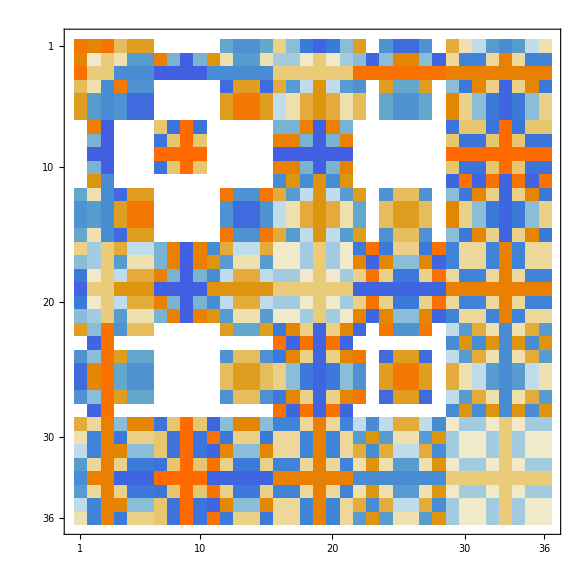

```mathematica
S=Array[(1/(√(2(k+2)))Sin[(π(W[[#1,1]]+1)(W[[#2,1]]+1))/(k+2)] ⅇ^(-ⅈ π (W[[#1,2]]W[[#2,2]])/(k+2)))&,{Length[W],Length[W]}]//Simplify;
S//MatrixPlot
```